# Coriolis Force on a Hockey Puck

First we’ll trace the path of a puck sliding with a velocity in the y direction (no x velocity) in a fixed frame. Now, lets rotate the circular surface beneath the puck. What does the path of the puck look like in this rotating frame? Let’s see what it looks like:

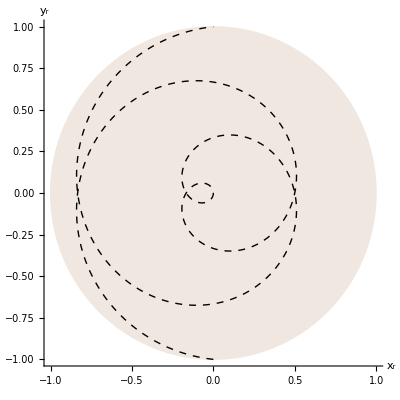

```mathematica
vx=0;
vy=0.1061;
x[t_]:= vx*t *Cos[t]+(vy*t-1)Sin[t];
y[t_] := (vy*t-1)Cos[t]- vx*t*Sin[t];Show[Graphics[{EdgeForm[Thick],LightBrown,Disk[{0,0},1]},Axes->True,AxesLabel->{"x_r","y_r"}],ParametricPlot[{x[t],y[t]},{t,0,6π}, PlotStyle->{Black, Thick, Dashed}]]
```

Pretty cool! We see that “something” must be “acting” on the puck from this perspective--something is causing the puck to accelerate because it definitely doesn’t have a constant velocity in a constant direction. This condition for a force arises purely artificially, since we are examining a non-inertial reference frame. 

Now let’s take this and make a nice animation!

```mathematica
RotatingFrame=Animate[Show[Graphics[{EdgeForm[Thick],Blend[{Green,Blue},.5],Disk[{0,0},1]},Axes->True,AxesLabel->{"x_r","y_r"}],ParametricPlot[{x[t],y[t]},{t,0,n}, PlotStyle->{Black, Thick, Dashed}], Graphics[{EdgeForm[Thick],Yellow,Disk[{x[n],y[n]},.1]}]],{n,0,6π}, AnimationRate->.05];

xf[t_]:=vx*t;
yf[t_]:=vy*t-1;

FixedFrame=Animate[
Show[
Graphics[
GeometricTransformation[{EdgeForm[Thick],Blend[{Red,White},.7],Disk[{0,0},1],Thick,Black,Line[{{-1,0},{1,0}}],Thick,Black,Line[{{0,-1},{0,1}}]},RotationTransform[n]],Axes->True, AxesLabel->{"x_f","y_f"},PlotRange->{{-1,1},{-1,1}}]
,ParametricPlot[{xf[t],yf[t]},{t,0,n}, PlotStyle->{Black, AbsoluteThickness[8]}],ParametricPlot[{xf[t],yf[t]},{t,0,n}, PlotStyle->{LightPurple, AbsoluteThickness[5]}],
Graphics[{EdgeForm[Thick],LightBlue,Disk[{xf[n],yf[n]},.1]}]]
,{n,0,6π}];
```

```mathematica
BothFrames=Animate[Flatten[GraphicsGrid[{{Show[Graphics[{EdgeForm[Thick],Blend[{Green,Blue},.5],Disk[{0,0},1]},Axes->False,AxesLabel->{"x_r","y_r"}],ParametricPlot[{x[t],y[t]},{t,0,n}, PlotStyle->{Black, Thick, Dashed}], Graphics[{EdgeForm[Thick],Yellow,Disk[{x[n],y[n]},.1]}]],Show[Graphics[GeometricTransformation[{EdgeForm[Thick],Blend[{Red,White},.7],Disk[{0,0},1],Thick,Black,Line[{{-1,0},{1,0}}],Thick,Black,Line[{{0,-1},{0,1}}]},RotationTransform[n]],Axes->False, AxesLabel->{"x_f","y_f"},PlotRange->{{-1,1},{-1,1}}]
,ParametricPlot[{xf[t],yf[t]},{t,0,n}, PlotStyle->{Black, AbsoluteThickness[8]}],
ParametricPlot[{xf[t],yf[t]},{t,0,n}, PlotStyle->{LightPurple, AbsoluteThickness[5]}],
Graphics[{EdgeForm[Thick],LightBlue,Disk[{xf[n],yf[n]},.1]}]]}}],1]
,{n,0,6π},AnimationRate->.1]
```

The puck slides along as seen from the rotating frame on the left (teal-yellow), and on the right is the fixed frame animation (pink-purple). The black cross on the pink surface helps one see the rotation of the surface beneath the puck.  (Can put axes in by changing “Axes → False” to “Axes → True”).